```mathematica
f=Nest[(1-t) #[[1]]+t #[[2]]&/@Partition[#,2,1]&,#,Length@#-1]&
```

Nest[((1-t) #1⟦1⟧+t #1⟦2⟧&)/@Partition[#1,2,1]&,#1,Length[#1]-1]&

```mathematica
f@{{0,0},{2,0},{0,2},{4,2}}
```

{{4 (1-t)^2 t+t (2 (1-t)^2+4 t^2),2 (1-t) t^2+t (2 (1-t) t+t (2 (1-t)+2 t))}}

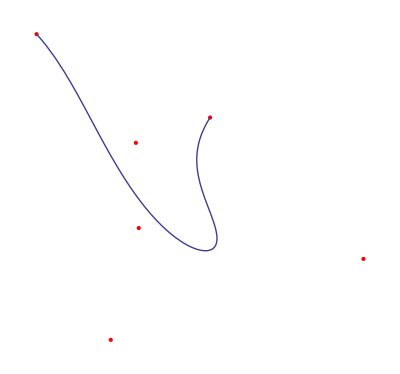

```mathematica
p=RandomReal[1,{6,2}];
Framed@Show[Graphics[{Red,PointSize[Large],Point@p}],ParametricPlot[f@p,{t,0,1},Axes->True]]
```

```mathematica
p=RandomReal[1,{4,3}];
Framed@Show[Graphics3D[{Red,PointSize[Large],Point@p}],ParametricPlot3D[f[p],{t,0,1},Axes->True]]
```

-Graphics3D-